```mathematica
Directory[]
```

C:\Users\Prajwal\Documents

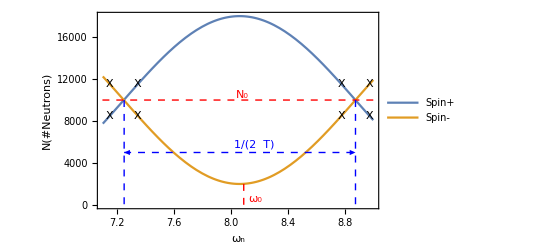

```mathematica
lineStyle={Thin,Red,Dashed};
line11=Line[{{7,10000},{9.5,10000}}];
line12=Line[{{8.09,2000},{8.09,-2000}}];
lineStyle2={Thin,Blue,Dashed};
lineStyle3={Thick,Black};
line21=Line[{{8.875,10000},{8.875,-2000}}];
line22=Line[{{7.25,10000},{7.25,-2000}}];
pt1[xx_]:=N[10000(1+0.8Cos[3-7(xx*8/29)])];
pt2[xx_]:=N[10000(1-0.8Cos[3-7(xx*8/29)])];
exp1=Plot[{pt1[xx],pt2[xx]},{xx,7.1,9},Frame->True,Axes->False,
Epilog->{
{Directive[lineStyle],line11,line12,Text[Style["N_0",FontSize->Large],{29.3*8/29,10500}],Text[Style["ω_0",FontSize->Large],{29.62*8/29,550}]},
{Directive[lineStyle2],line21,line22,{Arrowheads[{-.02,.02}],Arrow[{{7.25,5000},{8.875,5000}}]},Text[Style["1/(2  T)",FontSize->Large],{29.6*8/29,5750}]},
{Directive[lineStyle3],Text[Style["X",FontSize->Large],{7.15,11500}],Text[Style["X",FontSize->Large],{7.15,8500}],Text[Style["X",FontSize->Large],{7.345,8500}],Text[Style["X",FontSize->Large],{7.345,11500}],(**)Text[Style["X",FontSize->Large],{8.78,8500}],Text[Style["X",FontSize->Large],{8.78,11500}],Text[Style["X",FontSize->Large],{8.97,11500}],Text[Style["X",FontSize->Large],{8.97,8500}]}
},
FrameLabel->{"ω_n","N(#Neutrons)"},TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},PlotLegends->{"Spin+","Spin-"},ImageSize->{1000}]
```

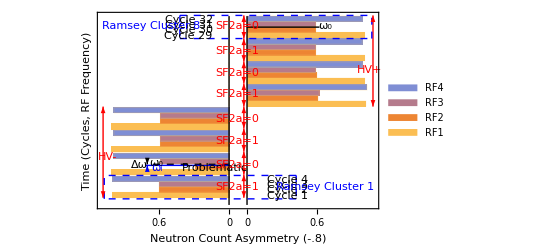

```mathematica
text=Table[0,{k,1,9}];
text[[1]]=Text[Rotate[Style["Problematic",FontSize->Medium],0 Degree],{-.2000,6}];
text[[2]]=Text[Rotate[Style["Cycle 29",FontSize->Medium],0 Degree],{-.4250,30.25}];
text[[3]]=Text[Rotate[Style["Cycle 30",FontSize->Medium],0 Degree],{-.4250,31.25}];
text[[4]]=Text[Rotate[Style["Cycle 31",FontSize->Medium],0 Degree],{-.4250,32.25}];
text[[5]]=Text[Rotate[Style["Cycle 32",FontSize->Medium],0 Degree],{-.4250,33.25}];
text[[6]]=Text[Rotate[Style["Cycle 1",FontSize->Medium],0 Degree],{.4250,.85}];
text[[7]]=Text[Rotate[Style["Cycle 2",FontSize->Medium],0 Degree],{.4250,1.85}];
text[[8]]=Text[Rotate[Style["Cycle 3",FontSize->Medium],0 Degree],{.4250,2.85}];
text[[9]]=Text[Rotate[Style["Cycle 4",FontSize->Medium],0 Degree],{.4250,3.85}];
arrow=Table[0,{k,1,12}];
arrow[[1]]={Directive[{Thin,Red}],Arrowheads[{-.01,.01}],Arrow[{{0.05,29.75},{0.05,34}}],Rotate[Text[Style["SF2a=0",FontSize->Medium],{-.01,32}],0 Degree]};
arrow[[2]]={Directive[{Thin,Red}],Arrowheads[{-.01,.01}],Arrow[{{0.05,29.75},{0.05,25.5}}],Rotate[Text[Style["SF2a=1",FontSize->Medium],{-.01,27.5}],0 Degree]};
arrow[[3]]={Directive[{Thin,Red}],Arrowheads[{-.01,.01}],Arrow[{{0.05,25.5},{0.05,21.5}}],Rotate[Text[Style["SF2a=0",FontSize->Medium],{-.01,23.5}],0 Degree]};
arrow[[4]]={Directive[{Thin,Red}],Arrowheads[{-.01,.01}],Arrow[{{0.05,21.5},{0.05,17.25}}],Rotate[Text[Style["SF2a=1",FontSize->Medium],{-.01,19.5}],0 Degree]};
arrow[[5]]={Directive[{Thin,Red}],Arrowheads[{-.01,.01}],Arrow[{{0.05,17.25},{0.05,13.25}}],Rotate[Text[Style["SF2a=0",FontSize->Medium],{-.01,15}],0 Degree]};
arrow[[6]]={Directive[{Thin,Red}],Arrowheads[{-.01,.01}],Arrow[{{0.05,13.25},{0.05,9}}],Rotate[Text[Style["SF2a=1",FontSize->Medium],{-.01,11}],0 Degree]};
arrow[[7]]={Directive[{Thin,Red}],Arrowheads[{-.01,.01}],Arrow[{{0.05,9},{0.05,4.75}}],Rotate[Text[Style["SF2a=0",FontSize->Medium],{-.01,6.5}],0 Degree]};
arrow[[8]]={Directive[{Thin,Red}],Arrowheads[{-.01,.01}],Arrow[{{0.05,4.75},{0.05,0.5}}],Rotate[Text[Style["SF2a=1",FontSize->Medium],{-.01,2.5}],0 Degree]};
arrow[[9]]={Directive[{Thin,Red}],Arrowheads[{-.01,.01}],Arrow[{{1.16,34},{1.16,17.25}}],Rotate[Text[Style["HV+",FontSize->Medium],{1.13,24}],0 Degree]};
arrow[[10]]={Directive[{Thin,Red}],Arrowheads[{-.01,.01}],Arrow[{{-1.16,0.5},{-1.16,17.25}}],Rotate[Text[Style["HV-",FontSize->Medium],{-1.125,8}],0 Degree]};
arrow[[11]]={Directive[{Thin,Black}],Arrowheads[{-.0,.01}],Arrow[{{-.78,7.65},{-.78,6.65}}],Rotate[Text[Style["Δω",FontSize->Medium],{-0.85,6.5}],0 Degree]};
arrow[[12]]={Directive[{Thin,Blue}],Arrowheads[{-.0,.01}],Arrow[{{-.78,5.45},{-.78,6.45}}]};
lines=Table[0,{k,1,3}];
lines[[1]]={Directive[{Thick,Black}],Text[Rotate[Style["ω_0",FontSize->Medium],0 Degree],{.7500,32}],Line[{{.0750,31.85},{.7000,31.85}}]};
lines[[2]]={Directive[{Thin,Black,Dashed}],Text[Rotate[Style["ω_0",FontSize->Medium],0 Degree],{-.700,6.95}],Line[{{-.0750,6.65},{-.8000,6.65}}]};
lines[[3]]={Directive[{Thin,Blue}],Text[Rotate[Style["ω_i",FontSize->Medium],0 Degree],{-.700,6}],Line[{{-.0750,6.45},{-.8000,6.45}}]};
box1={Directive[{Thin,Blue,Dashed}],Text[Rotate[Style["Ramsey Cluster 8",FontSize->Large],0 Degree],{-.7500,32}],Line[{{-.5000,29.75},{1.1500,29.75}}],Line[{{1.1500,29.75},{1.1500,34}}],Line[{{-.5000,34},{1.1500,34}}],Line[{{-.5000,34},{-.5000,29.75}}]};
box2={Directive[{Thin,Blue,Dashed}],Text[Rotate[Style["Ramsey Cluster 1",FontSize->Large],0 Degree],{.7500,2.5}],Line[{{.5000,.3},{-1.1500,.3}}],Line[{{-1.1500,.3},{-1.1500,4.6}}],Line[{{.5000,4.6},{-1.1500,4.6}}],Line[{{.5000,4.6},{.5000,.3}}]};
PairedBarChart[0.01{{100,60,60,100},{101,29,59,99},{101,59,59,99},{101,59,59,99},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},0.01{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{102,61,62,103},{101,60,59,99},{101,59,59,99},{101,59,59,99}},Frame->True,FrameLabel->{"Neutron Count Asymmetry (-.8)","Time (Cycles, RF Frequency)"},TicksStyle->Directive[FontSize->40],ChartLegends->{"RF1","RF2","RF3","RF4"},LabelStyle->{18},Epilog->Join[lines,text,arrow,box1,box2],ImageSize->{1000}]
```

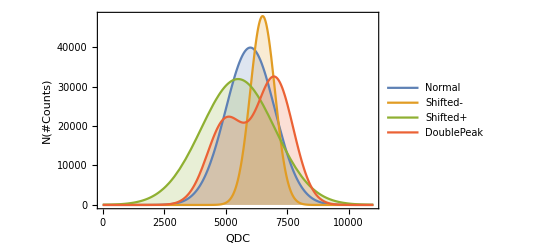

```mathematica
Plot[{10^8 PDF[NormalDistribution[6000,1000],xx],0.6 10^8 PDF[NormalDistribution[6500,500],xx],1.2 10^8 PDF[NormalDistribution[5500,1500],xx],4 10^7 PDF[NormalDistribution[5000,750],xx]+6 10^7 PDF[NormalDistribution[7000,750],xx]},{xx,0,11000},Frame->True,PlotRange->Full,(*Epilog->{{Directive[lineStyle],line11,line12,Text[Style["N_0",FontSize->Large],{29.7,6100}],Text[Style["ω_0",FontSize->Large],{30.05,4500}]}},*)FrameLabel->{"QDC","N(#Counts)"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},PlotLegends->{"Normal","Shifted-","Shifted+","DoublePeak"},Filling->Axis,ImageSize->{1000}]
```

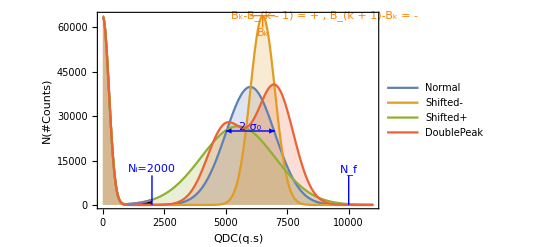

```mathematica
lineStyle={Thin,Blue};
lineStyle2={Thin,Orange};
line11=Line[{{2000,0},{2000,10000}}];
line12=Line[{{10000,0},{10000,10000}}];
line13=Line[{{6000,64000},{7000,64000}}];
line14=Line[{{6500,64000},{6500,60000}}];
Plot[{(2 10^7 PDF[HalfNormalDistribution[.005],xx]+10^8 PDF[NormalDistribution[6000,1000],xx]),(2 10^7 PDF[HalfNormalDistribution[.005],xx]+0.8 10^8 PDF[NormalDistribution[6500,500],xx]),(2 10^7 PDF[HalfNormalDistribution[.005],xx]+10^8 PDF[NormalDistribution[5500,1500],xx]),(2 10^7 PDF[HalfNormalDistribution[.005],xx]+5 10^7 PDF[NormalDistribution[5000,750],xx]+7.5  10^7 PDF[NormalDistribution[7000,750],xx]),Piecewise[{{(2 10^7 PDF[HalfNormalDistribution[.005],xx]+10^8 PDF[NormalDistribution[5500,1500],xx]),1000≤xx≤2000}},_]},{xx,0,11000},Frame->True,PlotRange->Full,Epilog->{{Directive[lineStyle],line11,line12,{Arrowheads[{-.02,.02}],Arrow[{{5000,25000},{7000,25000}}]},Text[Style["2 σ_0",FontSize->Large],{6000,26500}],Text[Style["N_i=2000",FontSize->Large],{2000,12000}],Text[Style["N_f",FontSize->Large],{10000,12000}]},{Directive[lineStyle2],line13,line14,Text[Style["B_k-B_(k - 1) = + , B_(k + 1)-B_k = -",FontSize->Large],{9000,64000}],Text[Style["B_k",FontSize->Large],{6500,58000}]}},FrameLabel->{"QDC(q.s)","N(#Counts)"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},PlotLegends->{"Normal","Shifted-","Shifted+","DoublePeak"},Filling->{1->Axis,2->Axis,5->{Axis,Black},4->Axis,3->Axis},ImageSize->{1000}]
```

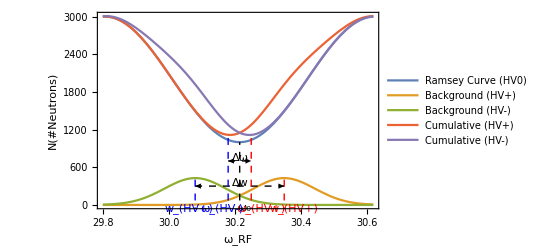

```mathematica
lineStyle={Thin,Black,Dashed};
line11=Line[{{30.215,-150},{30.215,1000}}];
lineStyle2={Thin,Blue,Dashed};
line21=Line[{{30.18,-150},{30.18,1120}}];
line22=Line[{{30.08,-150},{30.08,450}}];
lineStyle3={Thin,Red,Dashed};
line31=Line[{{30.25,-150},{30.25,1120}}];
line32=Line[{{30.35,-150},{30.35,450}}];
pt1[xx_]:=2000+1000Cos[3.1235941364458886-7.693489520741468 xx];
pt2[xx_]:=(10^(2)*PDF[SkewNormalDistribution[30.315,.1,.5],xx]);
pt3[xx_]:=(10^(2)*PDF[SkewNormalDistribution[30.115,.1,-.5],xx]);
pt4[xx_]=(pt1[xx]+pt2[xx])/1;
pt5[xx_]=(pt1[xx]+pt3[xx])/1;
exp1=Plot[{pt1[xx],pt2[xx],pt3[xx],pt4[xx],pt5[xx]},{xx,29.8,30.62},Frame->True,Epilog->{{Directive[lineStyle],line11,Text[Style["ω_0",FontSize->Large],{30.23,-50}],Text[Style["Δω",FontSize->Large],{30.218,750}],Text[Style["Δw",FontSize->Large],{30.218,350}],{Arrowheads[{-.02,.02}],Arrow[{{30.18,700},{30.25,700}}]},{Arrowheads[{-.02,.02}],Arrow[{{30.08,300},{30.35,300}}]}},{Directive[lineStyle3],line31,line32,Text[Style["ω_(HV+)",FontSize->Large],{30.28,-50}],Text[Style["w_(HV+)",FontSize->Large],{30.38,-50}]},{Directive[lineStyle2],line21,line22,Text[Style["w_(HV+)",FontSize->Large],{30.06,-50}],Text[Style["ω_(HV-)",FontSize->Large],{30.16,-50}]}},FrameLabel->{"ω_RF","N(#Neutrons)"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},PlotLegends->{"Ramsey Curve (HV0)","Background (HV+)","Background (HV-)","Cumulative (HV+)","Cumulative (HV-)"},ImageSize->{1000}]
```